# Moiré Pattern

Creating an interference pattern by overlaying similar but slightly offset templates

Manan Aggarwal, Jun 28,  2018

In physics, mathematics, and art, a moiré pattern is a secondary and visually evident superimposed pattern created, for example, when two identical patterns on a flat or curved surface (such as closely spaced straight lines drawn radiating from a point or taking the form of a grid) are overlaid. In the following sections we will see how to create these patterns in Wolfram Language and explore some of its applications.

## Pattern Formation

Moiré patterns can be easily generated in Wolfram Language through a variety of ways; here are a few:

Create a moire pattern by superimposing grids inclined at a fixed angle:

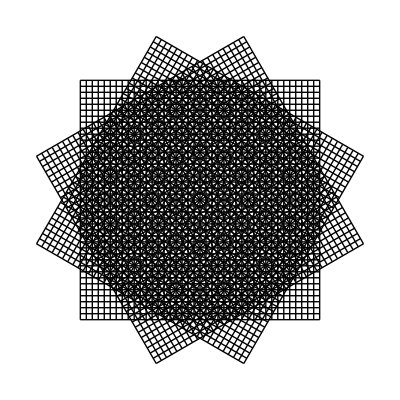

```mathematica
lines[t_,n_] := Line /@ ({RotationMatrix[t].# &/@ {{-1,#}, {1,#}},
	RotationMatrix[t].# &/@ {{#,-1}, {#,1}}} &/@ Range[-1,1,2/n]) // Graphics;
lines[#,40] &/@ Range[0, π-π/3, π/3] // Show
```

In the above example, the angle between each grid is π/3 radians.

Create an interactive visual of a moire pattern with adjustable number of grids:

```mathematica
grid = Graphics@GraphicsGroup[
	Table[
		{Line[{{x,-5},{x,5}}],
		Line[{{-5,x},{5,x}}]},
		{x,-5,5,.25}]
	];
Manipulate[
	Overlay[
		Table[
			Rotate[grid,i .2], {i,-n,n}
			],
		Alignment->Center
		],
	{n,0,5}]
```

Here we use Manipulate to modify the number of grids.

Create an interactive visual of a moire pattern with variable angles of rotation:

```mathematica
Manipulate[
	Overlay[
		Table[
			Rotate[grid,i θ], {i,-2,2}
			],
		Alignment->Center],
	{θ,0,π/12}]
```

Again, we use Manipulate to control the relative inclination of grids.

One can further play with these parameters to overlay grids with small relative angles:

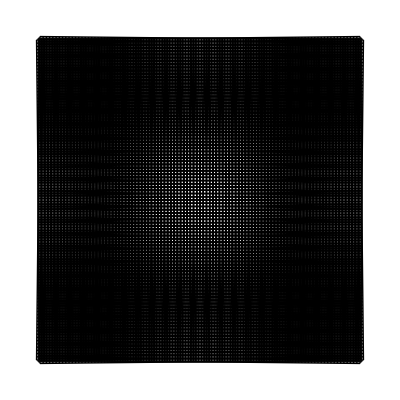

```mathematica
lines[#, 100] & /@ Range[-π/300, π/300, π/300] // Show
```

Or randomise the spacing and angle of each grid:

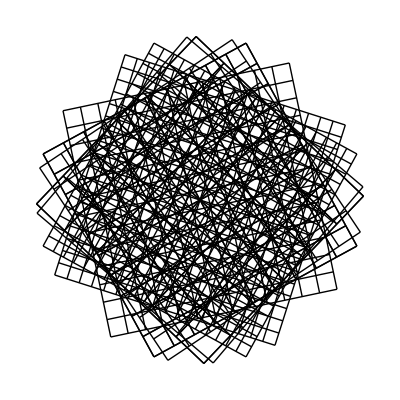

```mathematica
lines[Cos[# π/30], #] & /@ RandomInteger[{1, 20}, 9] // Show
```

## Calculations

Let us consider two patterns with the same step p, but the second pattern is rotated by an angle θ. When seen from afar, we can also see darker and lighter lines: the light lines correspond to the lines passing through the intersections of the two patterns.
If we consider a cell of the lattice formed, we can see that it’s a rhombus with each equal to

d = p/(sin θ)

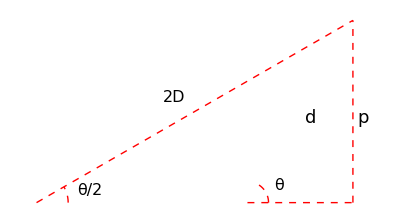

```mathematica
p0 = {0,0};
u0 = {0.5,Sqrt[3]/2};
v0 = {1,0};
ill={EdgeForm[Thick],Red,Dashed,Line[{{v,{1.5,0}},{{1.5,0},u0+v0},{p0,u0+v0}}], Circle[{1,0},0.1,{0 Degree,60 Degree}], Circle[{0,0},0.15,{0 Degree,30 Degree}]};
Graphics[{EdgeForm[Thick],White, Parallelogram[{0,0}, {u0,v0}], ill, Text[Style["2D",16, Black],{.65,0.5}], Text[Style["d",18, Black],{1.30,0.4}], Text[Style["p",18, Black],{1.55,0.4}], Text[Style["θ",16, Black],{1.15,0.08}], Text[Style["θ/2",16, Black],{.25,0.06}]}]
```

Let D be the spacing between two light lines. Then the long diagonal is 2 D. 
The Pythagorean theorem gives:

(2D)^2 = d^2 (1+cosθ)^2 + p^2
(2D)^2 = p^2/(sin^2 θ)(1+cosθ)^2 + p^2
(2D)^2 = p^2.((1+cosθ)^2/(sin^2 θ) + 1)
(2D)^2 = 2p^2.((1+cosθ)/(sin^2 θ))
  D = (p/2)/(sin θ/2)

When θ is very small (θ<π/6) the following approximations can be made:

sin θ ≈ θ
		cos θ ≈ 1

Thus,
		D ≈ p/θ

We can see that for smaller values of θ  the lighter lines are farther apart; when both patterns are parallel (θ = 0), the spacing between the lighter lines is infinite. This gives us two ways to determine θ: by the orientation of the lighter lines and by their spacing.

θ ≈ p/D

If we choose to measure the angle, the final error is proportional to the measurement error. If we choose to measure the spacing, the final error is proportional to the inverse of the spacing. Hence, for small angles, it is best to measure the spacing.

The illustration below demonstrates the effect of changing the angle between two sets of equidistant parallel lines.

```mathematica
parallel[n_] := Table[
	Line[
		{{-n,i}, {n,i}}
		], {i,-n,n}];
Manipulate[
	Graphics[
		{parallel[m], Rotate[parallel[n],θ]}], {m,40,100}, {n,40,100}, {θ,0,Pi}]
```

This visual effect can also be replicated for curved lines.

Drag the slider to change the number of concentric circles. Move the pointer to change the relative position of the circles.

```mathematica
curved[n_, cen_] := Graphics[
	Table[
		Circle[
			cen, Rescale[i,{0, n}, {1, 0}]], {i, 0, n}
	]];
Manipulate[
	Show[
		curved[n, {0, 0}], curved[n, x]
	], 
	{n, 1, 100}, {x, {-1, -1}, {1, 1}}
]
```

## Implications and Applications

Moiré patterns are produced in an astonishing variety of contexts in nature. Examples include the patterns of shifting dark bands seen in window screens and the shifting patterns observed when moving past overlapping chain link fences. In both cases, small motions of the two patterns relative to each other create large changes in the overall pattern observed. The interference patterns produced by light, sound, or any other wave-type behavior are moiré patterns. Among other things, researchers use this effect to map the topography of surfaces. By placing known patterns on the surfaces using light and analyzing the resulting moiré pattern from the reflections, the shape of the surface can be determined. This technique is used to obtain critical information about the rotational orientation and electronic properties of graphene.

Create a rotational image of bilayer graphene:

```mathematica
segment = Disk[#,1/3] &/@ CirclePoints[6][[2;;5]];
layer = Translate[segment,
	Join@@Array[{3 #,1.76 #2}&,{10,17},0]];
Manipulate[
	Graphics[
		{Blue,layer,Darker@Red,Rotate[layer,-θ]},
		PlotRange->{{-7,35},{-7,35}},
		ImageSize->500],
	{{θ,0.55},0,Pi/2}]
```

## Further Exploration

Moiré patterns are an interesting subject to study and play with. Moving one pattern over another can generate fascinating visual effects. We encourage the reader to experiment with the grids provided below and explore more patterns themselves.

```mathematica
img = SetAlphaChannel[
	Image[lines[0,40]], ColorNegate[Image[lines[0,40]]]
	];
GraphicsGrid[{{img,img}, {img,img}}]
```

-Graphics-

If you’re interested in learning more about the nature of moiré patterns you might want to check out wave interference.

## Author Contact Information

Email: maggarw7@jhu.edu